# Initialization

```mathematica
$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]

Off[PrintAsCharacter::argx];

NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
```

# Teukolsky Kinnersely projection consistency tests

## T_nn

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,data["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tnnSymbolic = {t,r,θ,ϕ}|->Evaluate@Tnn[SampleData, AsSymbolic->True];
tnnOptimized = Tnn[SampleData, AsOptimized->True];
tnnInterpolating = Tnn[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tnn takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50},
Print["Fractional difference between Optimized form of Tnn and Symbolic form at (r,θ)=(50,π/2):"];
((tnnOptimized[0,radialpoint,θpoint,0]-tnnSymbolic[0,radialpoint,θpoint,0])/tnnSymbolic[0,radialpoint,θpoint,0])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tnn and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tnn and the InterpolationFunction form at θ=π/2:"];
Plot[(tnnInterpolating[Ttest,r,θpoint,ϕtest]-tnnOptimized[Ttest,r,θpoint,ϕtest])/tnnOptimized[Ttest,r,θpoint,ϕtest], {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

## T_(m̄ m̄)

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,SampleData["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tmbmbSymbolic = {t,r,θ,ϕ}|->Evaluate@Tmbmb[SampleData, AsSymbolic->True];
tmbmbOptimized = Tmbmb[SampleData, AsOptimized->True];
tmbmbInterpolating = Tmbmb[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tmbmb takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbmb and Symbolic form at (r,θ)=(50,π/2):"];
((tmbmbOptimized[Ttest,radialpoint,θpoint,ϕtest]-tmbmbSymbolic[Ttest,radialpoint,θpoint,ϕtest])/tmbmbSymbolic[Ttest,radialpoint,θpoint,ϕtest])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tmbmb and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbmb and the InterpolationFunction form at θ=π/2:"];
Plot[Abs@((tmbmbInterpolating[Ttest,r,θpoint,ϕtest]-tmbmbOptimized[Ttest,r,θpoint,ϕtest])/tmbmbOptimized[Ttest,r,θpoint,ϕtest]), {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

## T_(m̄ n)

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,data["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tmbnSymbolic = {t,r,θ,ϕ}|->Evaluate@Tmbn[SampleData, AsSymbolic->True];
tmbnOptimized = Tmbn[SampleData, AsOptimized->True];
tmbnInterpolating = Tmbn[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tmbn takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50},
Print["Fractional difference between Optimized form of Tmbn and Symbolic form at (r,θ)=(50,π/2):"];
((tmbnOptimized[0,radialpoint,θpoint,0]-tmbnSymbolic[0,radialpoint,θpoint,0])/tmbnSymbolic[0,radialpoint,θpoint,0])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tmbn and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbn and the InterpolationFunction form at θ=π/2:"];
Plot[Abs@((tmbnInterpolating[Ttest,r,θpoint,ϕtest]-tmbnOptimized[Ttest,r,θpoint,ϕtest])/tmbnOptimized[Ttest,r,θpoint,ϕtest]), {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

# Comparison to Nils Code

## Function by Function

## Vector Field

#### Numerical

```mathematica
testsol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv3_10m1η0n0l0s-1χ9_10KMax4branch1.mx"];
radialSolution = testsol["Solution", "R"];
angularSolution = testsol["Solution", "S"];


NotebookEvaluate[NotebookDirectory[]<>"NilsFunctions.nb"];
GenerateNilsVectorField[testsol];

AupNils = Aupvector;
AdownNils = Adownvector;
AupNilsExplicit = OptimizedFunction[{t,r,θ,ϕ}, AupSimp/.solidentify/.parameters];
AdownNilsExplicit = OptimizedFunction[{t,r,θ,ϕ}, AdownSimp/.solidentify/.parameters];

ReprRule = {a->testsol["Parameters", "χ"]};
AupMe = FKKSProca[testsol, Optimized->True, RealPart->True, QuasiboundState->True];
With[{Ttest =RandomReal[{0,100}], RTest = RandomReal[{2,100}], θTest = RandomReal[{0,π}], ϕTest = RandomReal[{0,2*π}]},
Column[{
Row[{"(Ttest, Rtest, θtest, ϕtest) = "<>ToString@{Ttest, RTest, θTest, ϕTest}}],
Row[{
Row[{"My A^μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Interp A^μ: ", AupNils[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNils[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]]}]
}],
Row[{
Row[{"My A_μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,-sphericalchart}]/.ReprRule/.r[]->RTest/.θ[]->θTest, {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Interp A_μ: ", AdownNils[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNils[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}]/.ReprRule/.r->RTest/.θ->θTest, {i,0,3}]]}]
}],
Row[{
Row[{"My A^μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Explicit A^μ: ", AupNilsExplicit[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNilsExplicit[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]]}]
}],
Row[{
Row[{"My A_μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,-sphericalchart}]/.ReprRule/.r[]->RTest/.θ[]->θTest, {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Explicit A_μ: ", AdownNilsExplicit[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AdownNilsExplicit[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}]/.ReprRule/.r->RTest/.θ->θTest, {i,0,3}]]}]
}]
}]
]
```

#### Numerical (Explicit construction)

```mathematica
(*Generate analytic expressions, check theyre equal, then insert numerical solution and recheck*)
testsol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
radialSolution = testsol["Solution", "R"];
angularSolution = testsol["Solution", "S"];
AupMeSymb = FKKSProca[analytic];
AupMeSymbTable = Table[AupMeSymb[{i,sphericalchart}], {i,0,3}];
AupNilsSymb = Import[NotebookDirectory[]<>"AupSimp.mx"]/.Re[x_]->x/.Im[x_]->0;

SymbolicCheck = Simplify[(AupNilsSymb-AupMeSymbTable)/.χ->a/.iν->νi/.rν->νr//FromxActVariables, TimeConstraint->Infinity];
If[TrueQ[SymbolicCheck!={0,0,0,0}], Print["Error: Symbolic expressions dont agree"]];
```

Replacement Rules

```mathematica
ApplyRealSolutionSet[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			ωr -> Re[solution["Solution","ω"]],
			ωi->Im[solution["Solution","ω"]],
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutωi[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			ωr -> Re[solution["Solution","ω"]],
			ωi->0,
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutProperDerivative[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]],
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]],
			ωr -> Re[solution["Solution","ω"]],
			ωi->Im[solution["Solution","ω"]],
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutProperDerivativeWithoutωi[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]],
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]],
			ωr -> Re[solution["Solution","ω"]],
			ωi->0,
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
```

```mathematica
AupMeNumeric = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]//Evaluate];
AupMeNumericWithoutωi = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutωi[testsol]//Evaluate];
AupMeNumericWithoutProperDerivative = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutProperDerivative[testsol]//Evaluate];
AupMeNumericWithoutProperDerivativeWithoutωi = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutProperDerivativeWithoutωi[testsol]//Evaluate];
AupMeNumericFromFunction = FKKSProca[testsol, Optimized->True, QuasiboundState->True];
Block[{
Rad = testsol["Solution", "R"],
dRad = Derivative[1][testsol["Solution", "R"]],
ddRad = Derivative[2][testsol["Solution", "R"]],
Sangl = testsol["Solution", "S"],
dSangl = Derivative[1][testsol["Solution", "S"]],
ddSangl = Derivative[2][testsol["Solution", "S"]],
},
parameters={χ->testsol["Parameters", "χ"],m->testsol["Parameters", "m"],rν->Re@testsol["Solution", "ν"],iν->Im@testsol["Solution", "ν"],ωi->0,ωr->Re@testsol["Solution", "ω"],μ->testsol["Parameters", "μNv"],nh->testsol["Parameters", "n"]};
solidentify=Evaluate@{Ri[r_]->Im[Rad[r]],Rr[r_]->Re[Rad[r]],Ri'[r_]->Im[dRad[r]],Rr'[r_]->Re[dRad[r]],Rr''[r_]->Re[ddRad[r]],Ri''[r_]->Im[ddRad[r]],Si[θ_]->Im[Sangl[θ]],Sr[θ_]->Re[Sangl[θ]],Si'[θ_]->Im[dSangl[θ]],Sr'[θ_]->Re[dSangl[θ]],Sr''[θ_]->Re[ddSangl[θ]],Si''[θ_]->Im[ddSangl[θ]]};
AupNilsNumeric = OptimizedFunction[{t,r,θ,ϕ}, AupNilsSymb/.solidentify/.parameters];
]
```

```mathematica
With[{Ttest =RandomReal[{0,100}], RTest = RandomReal[{2,100}], θTest = RandomReal[{0,π}], ϕTest = RandomReal[{0,2*π}]},
Column[{
Row[{"AupNils: ", Spacer[255],AupNilsNumeric[Ttest, RTest, θTest, ϕTest]}],
Row[{"Aupme: ", Spacer[270], AupMeNumeric[Ttest, RTest, θTest, ϕTest]}],
Row[{"Aupme From Function: ", Spacer[161], AupMeNumericFromFunction[Ttest, RTest, θTest, ϕTest][[1]]}],
Row[{"AupMe Without Proper Derivative: ", Spacer[67], AupMeNumericWithoutProperDerivative[Ttest, RTest, θTest, ϕTest]}],
Row[{"AupMe Without Proper Derivatve and ωi: ", Spacer[20], AupMeNumericWithoutProperDerivativeWithoutωi[Ttest, RTest, θTest, ϕTest]}],
Row[{"AupMe Without ωi: ", Spacer[183], AupMeNumericWithoutωi[Ttest, RTest, θTest, ϕTest]}]
}]
]
```

#### Analytic

Polarization Tensor

```mathematica
NilsPolarization = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Debugging/NilsPolarizationTensor.mx"];
MyPolarization = Table[Polarization[{i,sphericalchart},{j,sphericalchart}], {i,0,3},{j,0,3}]/.a->χ/.r[]->r;
Simplify[NilsPolarization-MyPolarization]
```

Vector field (Full)

```mathematica
ProcaFieldMine = Table[FKKSProca[analytic, RealPart->False][{i,sphericalchart}], {i,0,3}]//FromxActVariables;
ProcaFieldNils = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Debugging/NilsFullsAupSimp.mx"]//FromxActVariables;
Simplify[ProcaFieldNils-ProcaFieldMine]
```

Vector Field (Real part)

```mathematica
AupNils = Import[NotebookDirectory[]<>"../../../NilsSiemonsenCode/OG_Code_MyExecution/Expressions/AupSimp.mx"];
AupMine = Import[NotebookDirectory[]<>"../Expressions/AuprealComponents.mx"];
AupMineCalculated =Table[ FKKSProca[analytic, RealPart->True][{i,sphericalchart}], {i,0,3}]/.χ->a;
ToMyVariables={iν->νi,rν->νr,χ->a,θ[]->θ,ϕ[]->ϕ,r[]->r,t[]->t};
AupNils=AupNils/.ToMyVariables/.Im[x_]->0/.Re[x_]->x;
AupMine=AupMine/.ToMyVariables;
res=Simplify[AupNils-AupMine];
res2 = Simplify[(AupMineCalculated-AupMine)/.χ->a//FromxActVariables];
If[TrueQ[res!={0,0,0,0}]||TrueQ[res2!={0,0,0,0}],Print["Not equal!"], Print["Results agree."]]
```

Results agree.

## Energy Momentum Tensor

### Arbitrary A_μ

```mathematica
TddNilsPrivate = Import[NotebookDirectory[]<>"../Debugging/TddNilsOwnGeneration.mx"];

Import[NotebookDirectory[]<>"../Packages/xActSetup.wl"];

PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNils = TddNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};

AFuncReprRule1 = Table[ToExpression["A"<>ToString[i]<>"[t[],r[],θ[],ϕ[]]"]->ToExpression["A"<>ToString[i]], {i,0,3}];
AFuncReprRule2 = Table[ToExpression["Derivative[1,___][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D0A"<>ToString[i]], {i,0,3}];
AFuncReprRule3 = Table[ToExpression["Derivative[_,1,___][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D1A"<>ToString[i]], {i,0,3}];
AFuncReprRule4 = Table[ToExpression["Derivative[___,1,_][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D2A"<>ToString[i]], {i,0,3}];
AFuncReprRule5 = Table[ToExpression["Derivative[___,1][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D3A"<>ToString[i]], {i,0,3}];
AFuncReprRule = Union[AFuncReprRule1, AFuncReprRule2, AFuncReprRule3, AFuncReprRule4,AFuncReprRule5];

DefScalarFunction[A0]; DefScalarFunction[A1]; DefScalarFunction[A2]; DefScalarFunction[A3];
A = CTensor[{A0[t[],r[],θ[],ϕ[]],A1[t[],r[],θ[],ϕ[]],A2[t[],r[],θ[],ϕ[]],A3[t[],r[],θ[],ϕ[]]}, {-sphericalchart}];
F =  Head[Cd[-ζ]@A[-ξ] - Cd[-ξ]@A[-ζ]];
tmp$ = F[-ζ,-γ]F[-ξ,γ] + μ^2*A[-ζ]A[-ξ] -1/4 met[-ζ,-ξ](F[-ι,-γ]F[ι,γ] + 2*μ^2*A[-γ]A[γ]);
EM = Head[tmp$];
EMlist = Table[EM[{i,-sphericalchart},{j,-sphericalchart}], {i,0,3},{j,0,3}]/.AFuncReprRule/.{r[]->r, θ[]->θ,a->χ};

Simplify[EMlist-TddNils]
```

### Arbitrary Z(t,r,θ,ϕ) = R(r)S(θ)e^(-iωt+imϕ)

```mathematica
testsol = getResults[$SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","1_5"}}]//First;

AMine = FKKSProca[analytic];
FMine = FKKSFieldStrength[analytic];

tmp$ = Head[FMine[-ζ,-γ]FMine[-ξ,γ] + μ^2*AMine[-ζ]AMine[-ξ] -1/4 met[-ζ,-ξ](FMine[-ι,-γ]FMine[ι,γ] + 2*μ^2*AMine[-γ]AMine[γ])];
TddMineOE= OptimizedFunction[{t,r,θ,ϕ}, tmp$[{0,-sphericalchart},{2,-sphericalchart}]/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]];

reprr = {μNv->1,μ->1,
		m->1, 
		a->0.5, χ->0.5,
		νi->1,iν->1, 
		νr->1,rν->1, 
		ωi->1, ωr->1};
TddMineSaved = Import[FileNameJoin[{$FKKSRoot, "Expressions", "FKKSEnergyMomentumRealCTensor.mx"}]];
TddMineSavedOE = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TddMineSaved[{0,-sphericalchart},{2,-sphericalchart}]//FromxActVariables//ApplyRealSolutionSet[testsol]]];


TddNilsPrivate = Import[FileNameJoin[{$FKKSRoot, "Debugging", "TddNilsOwnGeneration.mx"}]];
PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNilsSymb = TddNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};
ApplySolutionToNils = {Table[ToExpression["A"<>ToString[i]]->AMine[{i,-sphericalchart}], {i,0,3}], Table[ToExpression["D"<>ToString[j]<>"A"<>ToString[i]]->D[AMine[{i,-sphericalchart}], {t[],r[],θ[],ϕ[]}[[j+1]]], {i,0,3},{j,0,3}]}//Flatten;
TddNils = TddNilsSymb/.ToParamSymbols/.ApplySolutionToNils/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ}//ApplyRealSolutionSet[testsol];
TddNilsOE = OptimizedFunction[{t,r,θ,ϕ},TddNils[[1,3]]//ApplyRealSolutionSet[testsol]];

With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{Row[{"TddNils: ", Spacer[38],TddNilsOE[Ttest,Rtest,θtest,ϕtest]}],
Row[{"TddMine: ", Spacer[38],TddMineOE[Ttest,Rtest,θtest,ϕtest]}],
Row[{"TddMineSaved: ",TddMineSavedOE[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

## Energy Density

```mathematica
testsol = getResults[$SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","1_5"}}]//First;

AMine = FKKSProca[analytic];
FMine = FKKSFieldStrength[analytic];

tmp$ = Head[FMine[-ζ,-γ]FMine[-ξ,γ] + μ^2*AMine[-ζ]AMine[-ξ] -1/4 met[-ζ,-ξ](FMine[-ι,-γ]FMine[ι,γ] + 2*μ^2*AMine[-γ]AMine[γ])];
endenMe= OptimizedFunction[{t,r,θ,ϕ}, -tmp$[{0,sphericalchart},{0,-sphericalchart}]/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]];

reprr = {μNv->1,μ->1,
		m->1, 
		a->0.5, χ->0.5,
		νi->1,iν->1, 
		νr->1,rν->1, 
		ωi->1, ωr->1};
TddMineSaved = Import[NotebookDirectory[]<>"../Expressions/FKKSEnergyMomentumRealCTensor.mx"];
TddMineSavedOE = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TddMineSaved[{0,-sphericalchart},{2,-sphericalchart}]//FromxActVariables//ApplyRealSolutionSet[testsol]]];

TudNilsPrivate = Import[NotebookDirectory[]<>"Tud.mx"];
PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNilsSymb = TudNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};
ApplySolutionToNils = {Table[ToExpression["A"<>ToString[i]]->AMine[{i,-sphericalchart}], {i,0,3}], Table[ToExpression["D"<>ToString[j]<>"A"<>ToString[i]]->D[AMine[{i,-sphericalchart}], {t[],r[],θ[],ϕ[]}[[j+1]]], {i,0,3},{j,0,3}]}//Flatten;
TudNils = TddNilsSymb/.ToParamSymbols/.ApplySolutionToNils/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ}//ApplyRealSolutionSet[testsol];
endenNils = OptimizedFunction[{t,r,θ,ϕ},-TudNils[[1,1]]//ApplyRealSolutionSet[testsol]];


With[{Ttest = RandomReal[{0,10}], Rtest = RandomReal[{2,10}], θtest = RandomReal[{0,π}], ϕtest = RandomReal[{0,2*π}]},
With[{nils = endenNils[Ttest, Rtest, θtest, ϕtest], mine = endenMe[Ttest, Rtest, θtest, ϕtest]},
Column[{
Row[{"Sample Point: ","T="<>ToString[Ttest]," R="<>ToString@Rtest," θ="<>ToString@θtest," ϕ="<>ToString@ϕtest}],
Spacer[10],
Row[{"Nils energy density: ",nils}],
Row[{"My energy density: ", mine}],
Row[{"Difference: ", nils-mine}]
}]
]
]
```

## BH Evolution

```mathematica
TestSol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
MyNormalization = FKKSNormalization[TestSol, 1, Recalculate->True]
```

```mathematica
(*Nils*)
wr=TestSol["Solution", "ω"]//Re;
Mini=1;
min=TestSol["Parameters", "m"];
spinin = TestSol["Parameters", "χ"];
dimlesspin[Mbar_]:=min/(wr Mini Mbar) (1-1/Mbar)+spinin/Mbar^2;
omegahorizon[Mbar_]:=dimlesspin[Mbar]/(2Mbar Mini(1+Sqrt[1-dimlesspin[Mbar]^2]));
massoutputinM0units=prec@(Mbar/.NSolve[omegahorizon[Mbar]==wr/min,Mbar][[1]])Mini;
dimlessspinoutput=prec@dimlesspin[massoutputinM0units/Mini]; (*We need to divide by Mini here, because the chi takes in \bar{M}, rather than stuff in M0 units! But massoutput is written in M0 units!*)

Mfspinf=prec@{massoutputinM0units,dimlessspinoutput};

Column[{"Difference between Nils and mine:",
Row[{"Final Spin_mine: ", Spacer[38],MyNormalization["FinalSpin"]}],
Row[{"Final Spin_nils: ", Spacer[38],Mfspinf[[2]]}],
Row[{"Final mass_mine: ", Spacer[38],MyNormalization["FinalMass"]}],
Row[{"Final mass_nils: ", Spacer[38],Mfspinf[[1]]}]
}]
```

## Teukolsky Kinnersly Projections

```mathematica
TestSol = Import[NotebookDirectory[]<>"../Solutions/FullSolutionSetRunData_ϵ1_10000μNv11_100m3η0n0l2s-1χ9_10KMax4branch1.mx"];
TddMineOE = FKKSEnergyMomentum[TestSol, Optimized->True];
TddTable = Table[TddMineOE[t,r,θ,ϕ][{i,-sphericalchart},{j,-sphericalchart}], {i,0,3},{j,0,3}];
TnnMine = Tnn[TestSol, AsOptimized->True];
TmnMine = Tmbn[TestSol, AsOptimized->True];
TmmMine = Tmbmb[TestSol, AsOptimized->True];
spin = TestSol["Parameters", "χ"];
Procamass = TestSol["Parameters", "μNv"];
mTeu = 2*TestSol["Parameters", "m"];
ωTeu = 2*TestSol["Solution", "ω"]//Re;
rstart = TestSol["Solution", "R"]["Domain"][[1]][[1]]//HorizonCoordToRadial[#,spin]&;
rstop = TestSol["Solution", "R"]["Domain"][[1]][[2]]//HorizonCoordToRadial[#,spin]&;
slp=0.25; (*slope of the step function*)
θmesh=If[TestSol["Parameters", "m"]==1,49,If[TestSol["Parameters", "m"]==2,59,59]];
step[x_]:=π/(θmesh+1) ((θmesh+1)^2/2 Exp[slp(x-(θmesh+1)/2)])/((θmesh+1)+(θmesh+1)/2(Exp[slp(x-(θmesh+1)/2)]-1));
θrange=prec@step[Range[1,θmesh+1]];
θstart=prec@(θrange//First);
θstop=prec@(θrange//Last);


Σ=r[]^2+χ^2 Cos[θ[]]^2;
Δ=r[]^2-2 r[]+χ^2;
DefTensor[nK[ζ],ℳ];
DefTensor[mK[ζ],ℳ];
DefTensor[mbarK[ζ],ℳ];
nKtemp=1/(2Σ) {r[]^2+χ^2,-Δ,0,χ}//Simplify;
ComponentValue[nK[ζ]//ToBasis[sphericalchart]//ComponentArray,nKtemp];
mKtemp={I χ Sin[θ[]],0,1,I/Sin[θ[]]}/(Sqrt[2](r[]+I χ Cos[θ[]]))//Simplify;
ComponentValue[mK[ζ]//ToBasis[sphericalchart]//ComponentArray,mKtemp];
mbarKtemp={-I χ Sin[θ[]],0,1,-I/Sin[θ[]]}/(Sqrt[2](r[]-I χ Cos[θ[]]))//Simplify;
ComponentValue[mbarK[ζ]//ToBasis[sphericalchart]//ComponentArray,mbarKtemp];

prec=SetPrecision[#,15]&;
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};

para=prec@{χ->spin,μ->Procamass,mT->mTeu,ωT->ωTeu};
rmesh=99;
thmesh = θmesh;
rdatapoint[x_]:=(rstop-rstart)/((rmesh+1)^4-1) x^4+rstart-(rstop-rstart)/((rmesh+1)^4-1);
rrange=prec@rdatapoint[Range[1,rmesh+1]];
θrange=prec@Range[θstart,θstop,(θstop-θstart)/thmesh];

PrintTemporary["Generating Tij Explicits"];
tnnexpltemp=(nKtemp//.coordinates) . (TddTable . (nKtemp//.coordinates));
TnnExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tnnexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
tmnexpltemp=(nKtemp//.coordinates) . (TddTable . (mbarKtemp//.coordinates));
TmnExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tmnexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
tmmexpltemp=(mbarKtemp//.coordinates) . (TddTable. (mbarKtemp//.coordinates));
TmmExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tmmexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
```

```mathematica
With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{"Difference between Nils and mine:",
Row[{"T_nn: ", Spacer[38],TnnMine[Ttest,Rtest,θtest,ϕtest]-TnnExpl[Ttest,Rtest,θtest,ϕtest]}],
Row[{"T_(m̄): ", Spacer[38],TmnMine[Ttest,Rtest,θtest,ϕtest]-TmnExpl[Ttest,Rtest,θtest,ϕtest]}],
Row[{"T_(m̄): ", Spacer[38],TmmMine[Ttest,Rtest,θtest,ϕtest]-TmmExpl[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

## Teukolsky Source Term

### Explicit

```mathematica
Dynamic[$Messenger]
TestSol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv1_4m1η0n0l0s-1χ9_10KMax4branch1.mx"];
RenormedData =RenormalizeProcaSolution[TestSol, TestSol["Derived"]["Normalization"]["Normalization"]];
TestSol = RenormedData;
spin = TestSol["Parameters", "χ"];
Procamass = TestSol["Parameters", "μNv"];
mTeu = 2*TestSol["Parameters", "m"];
ωTeu = 2*TestSol["Solution", "ω"]//Re;
rstart = TestSol["Solution", "R"]["Domain"][[1]][[1]]//HorizonCoordToRadial[#,spin]&;
rstop = TestSol["Solution", "R"]["Domain"][[1]][[2]]//HorizonCoordToRadial[#,spin]&;
slp=0.25; (*slope of the step function*)
θmesh=If[TestSol["Parameters", "m"]==1,49,If[TestSol["Parameters", "m"]==2,59,59]];
step[x_]:=π/(θmesh+1) ((θmesh+1)^2/2 Exp[slp(x-(θmesh+1)/2)])/((θmesh+1)+(θmesh+1)/2(Exp[slp(x-(θmesh+1)/2)]-1));
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};
prec=SetPrecision[#,15]&;
θrange=prec@step[Range[1,θmesh+1]];
θstart=prec@(θrange//First);
θstop=prec@(θrange//Last);
rmesh=99;
thmesh=θmesh; (*This HAS to be an odd number to hit the last θstop exactly*)
rdatapoint[x_]:=(rstop-rstart)/((rmesh+1)^4-1) x^4+rstart-(rstop-rstart)/((rmesh+1)^4-1);
rrange=prec@rdatapoint[Range[1,rmesh+1]];
θrange=prec@Range[θstart,θstop,(θstop-θstart)/thmesh];

(*Nils*)
TeukolskyTintegrand1 = Import[NotebookDirectory[]<>"../Debugging/NilsTeuTintegrandOwnGeneration.mx"];

(*Compute Projections*)

TnnMine = Tnn[TestSol, AsInterpolatingFunction->True];
TmnMine = Tmbn[TestSol, AsInterpolatingFunction->True];
TmmMine = Tmbmb[TestSol, AsInterpolatingFunction->True];

(*Computing Teukolsky Source term for Nils*)
TijtoExpl=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprNils = Union[TijtoExpl,dTijtoExpl,ddTijtoExpl, {mT->mTeu,χ->spin,ωT->ωTeu}];
TeukolskySourceNils = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TeukolskyTintegrand1/.TotalReprNils]];

(*Mine*)
Block[{L,Jp},With[{
tmbmb = TmmMine,
tmbn = TmnMine,
tnn = TnnMine, 
ρ = Teukrho,
ρb = Teukrhob, 
Δ = KerrΔ},
L[s_][expr_]:=
	Block[{tmp},
		With[{EXPRESSION = FromxActVariables[expr]},
			tmp = (D[#,θ]- I/Sin[θ] D[#,ϕ]-I*a*Sin[θ]D[#,t]+s*Cot[θ]*#)&@EXPRESSION
			];
		ToxActVariables[tmp]
	];
Jp[expr_]:=
	Block[{tmp},
		With[{EXPRESSION = FromxActVariables[expr], Δ = FromxActVariables[KerrΔ]},
			tmp=(D[#,r]-1/Δ ((r^2+a^2)D[#,t]+a*D[#,ϕ]))&@EXPRESSION
		];
	ToxActVariables[tmp]
	];
B = -1/2 ρ^8*ρb*L[-1][ρ^-4*L[0][(ρ^-2*ρb^-1*tnn[t,r,θ,ϕ])]]-1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*L[-1][ρ^-4*ρb^2 Jp[(ρ^-2*ρb^-2*Δ^-1*tmbn[t,r,θ,ϕ])]];
BPrime = -1/4 ρ^8*ρb*Δ^2*Jp[ρ^-4*Jp[(ρ^-2*ρb*tmbmb[t,r,θ,ϕ])]]-1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*Jp[ρ^-4*ρb^2*Δ^-1*L[-1][(ρ^-2*ρb^-2*tmbn[t,r,θ,ϕ])]];
expr = (2(B+BPrime))//FromxActVariables//ApplySolutionSet[TestSol];
TeukolskySourceMine = OptimizedFunction[{t,r,θ,ϕ},Evaluate[expr]];
]
]
```

```mathematica
(*Compare*)
With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{"Difference between Nils and mine:",
Row[{"𝒯_Mine: ", Spacer[38],TeukolskySourceMine[Ttest,Rtest,θtest,ϕtest]}],
Row[{"𝒯_Nils: ", Spacer[38],TeukolskySourceNils[Ttest,Rtest,θtest,ϕtest]}],Row[{"𝒯: ", Spacer[38],TeukolskySourceNils[Ttest,Rtest,θtest,ϕtest]-TeukolskySourceMine[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

#### Generate Nils TeukolskySource

```mathematica
TnnMine = Tnn[TestSol, AsOptimized->True];
TmnMine = Tmbn[TestSol, AsOptimized->True];
TmmMine = Tmbmb[TestSol, AsOptimized->True];
TnnMineOp = Tnn[TestSol, AsInterpolatingFunction->True];
TmnMineOp = Tmbn[TestSol, AsInterpolatingFunction->True];
TmmMineOp = Tmbmb[TestSol, AsInterpolatingFunction->True];
TeukSourceMine = TeukolskySource[TestSol];
```

```mathematica
$Messenger="Generating: Tnn...";
tnntemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TnnMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tnntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumRe[rr_,θθ_]:=Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tnntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumIm[rr_,θθ_]:=Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TnnInter[rr_,θθ_]:=TnnInterNumRe[r,θ]+I TnnInterNumIm[r,θ]/.{r->rr,θ->θθ};

$Messenger="Generating: Tmn...";
tmntemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmnMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumRe[rr_,θθ_]:=Interpolation[tmntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumIm[rr_,θθ_]:=Interpolation[tmntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmnInter[rr_,θθ_]:=TmnInterNumRe[r,θ]+I TmnInterNumIm[r,θ]/.{r->rr,θ->θθ};

$Messenger="Generating: Tmm...";
tmmtemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmmMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmmtempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumRe[rr_,θθ_]:=Interpolation[tmmtempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmmtempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumIm[rr_,θθ_]:=Interpolation[tmmtempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmmInter[rr_,θθ_]:=TmmInterNumRe[r,θ]+I TmmInterNumIm[r,θ]/.{r->rr,θ->θθ};
Print["Generating: Done."];
```

```mathematica
(*tnntempRInterp = Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"];
tnntempIInterp = Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"];
tmntempRInterp = Interpolation[tmntempR,InterpolationOrder->3,Method->"Spline"];
tmntempIInterp = Interpolation[tmntempI,InterpolationOrder->3,Method->"Spline"];
tmmtempRInterp = Interpolation[tmmtempR,InterpolationOrder->3,Method->"Spline"];
tmmtempIInterp = Interpolation[tmmtempI,InterpolationOrder->3,Method->"Spline"];
Export[NotebookDirectory[]<>"tnntempRInterp.mx", tnntempRInterp]
Export[NotebookDirectory[]<>"tnntempIInterp.mx", tnntempIInterp]
Export[NotebookDirectory[]<>"tmntempRInterp.mx", tmntempRInterp]
Export[NotebookDirectory[]<>"tmntempIInterp.mx", tmntempIInterp]
Export[NotebookDirectory[]<>"tmmtempRInterp.mx", tmmtempRInterp]
Export[NotebookDirectory[]<>"tmmtempIInterp.mx", tmmtempIInterp]
*)
```

```mathematica
tnntempRInterp = Import[NotebookDirectory[]<>"tnntempRInterp.mx"];
tnntempIInterp = Import[NotebookDirectory[]<>"tnntempIInterp.mx"];
tmntempRInterp = Import[NotebookDirectory[]<>"tmntempRInterp.mx"];
tmntempIInterp = Import[NotebookDirectory[]<>"tmntempIInterp.mx"];
tmmtempRInterp = Import[NotebookDirectory[]<>"tmmtempRInterp.mx"];
tmmtempIInterp = Import[NotebookDirectory[]<>"tmmtempIInterp.mx"];
TnnInter = {r,θ}|->tnntempRInterp[r,θ]+I*tnntempIInterp[r,θ];
TmnInter = {r,θ}|->tmntempRInterp[r,θ]+I*tmntempIInterp[r,θ];
TmmInter = {r,θ}|->tmmtempRInterp[r,θ]+I*tmmtempIInterp[r,θ];
```

```mathematica
(*Computing integrand of Tlmω*)
TijtoExpl=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprNils = Union[TijtoExpl,dTijtoExpl,ddTijtoExpl];
TijtoExplMine=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExplMine=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExplMine=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprMine = Union[TijtoExplMine, dTijtoExplMine,ddTijtoExplMine];
TeukolskyTintegrand=Import[NotebookDirectory[]<>"NilsTeuTintegrandOwnGeneration.mx"];
TTtemp=(TeukolskyTintegrand/.{χ->spin,μ->Procamass,ωT->ωTeu,mT->mTeu}//.TotalReprMine);
TeukolskyTintegrandExpl[tt_,rr_,θθ_,ϕϕ_]:=TTtemp/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ};
```

```mathematica
TeukolskyTintegrandExpl[0,1500,1,0]
TeukSourceMine[0,1500,1,0]
```

### Analytic

```mathematica
ρ=1/(r-I χ Cos[θ]);
ρbar=1/(r+I χ Cos[θ]);
ReprRule = Table[ToExpression["PrivateTeukolsky`T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]],{j,{"nn","mn","mm"}}]∪Flatten@Table[ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["T"]<>ToString[j]]->ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]],{i,{1,2}},{j,{"nn","mn","mm"}}]∪Flatten@Table[ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]],{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}];
nils = (ρbar ρ^5)/2 Import[$FKKSRoot<>"/Debugging/NilsSiemonsenCode/OG_Code_MyExecution/Expressions/TeuTintegrand.mx"]/.{PrivateTeukolsky`t->t,PrivateTeukolsky`r->r,PrivateTeukolsky`θ->θ,PrivateTeukolsky`ϕ->ϕ, PrivateTeukolsky`χ->χ,PrivateTeukolsky`ωT->ωT, PrivateTeukolsky`mT->mT}/.ReprRule;
nilsinmine = nils/.χ->a/.ωT->2*ω/.mT->2*m/.Tnn->tnn[r,θ]/.Tmn->tmbn[r,θ]/.Tmm->tmbmb[r,θ]/.{d1d1Tmm->Derivative[2,0][tmbmb][r,θ],d1d2Tmn->Derivative[1,1][tmbn][r,θ],d1Tmm->Derivative[1,0][tmbmb][r,θ],d1Tmn->Derivative[1,0][tmbn][r,θ],d2d1Tmn->Derivative[1,1][tmbn][r,θ],d2d2Tnn->Derivative[0,2][tnn][r,θ],d2Tmn->Derivative[0,1][tmbn][r,θ],d2Tnn->Derivative[0,1][tnn][r,θ]}//FromxActVariables;


mine = With[{
ρ = Teukrho,
ρb = Teukrhob, 
Δ = KerrΔ
},
B111 = -1/2 ρ^8*ρb*Lexpl[-1][ρ^-4*Lexpl[0][(ρ^-2*ρb^-1*tnn[r,θ])]];
B222=(-1/(2*Sqrt[2])) ρ^8*ρb*Δ^2*Lexpl[-1][ρ^-4*ρb^2 Jpexpl[(ρ^-2*ρb^-2*Δ^-1*tmbn[r,θ])]];
B =B111 +  B222;
BPrime1 =  -1/4 ρ^8*ρb*Δ^2*Jpexpl[ρ^-4*Jpexpl[(ρ^-2*ρb*tmbmb[r,θ])]];
BPrime2 = -1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*Jpexpl[ρ^-4*ρb^2*Δ^-1*Lexpl[-1][(ρ^-2*ρb^-2*tmbn[r,θ])]];
BPrime =BPrime1 + BPrime2;
(2(B+BPrime))//FromxActVariables
];

FullSimplify[mine-nilsinmine]
```

## Teukolsky Source Modal

```mathematica
Subscript[𝒯, lmω]
```

```mathematica
Dynamic[$Messenger]
TestSol1 = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv1_4m1η0n0l0s-1χ9_10KMax4branch1.mx"];
TestSol2 = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
TestSol = TestSol2;
RenormedData =RenormalizeProcaSolution[TestSol, TestSol["Derived"]["Normalization"]["Normalization"]];
TestSol = RenormedData;
TlmwMine = TeukolskySourceModal[TestSol,2,2, Recalculate->True];
```

Generate Nils Tlmw

```mathematica
With[{lTeu=2},
thetarange=prec@Range[0+10^-4,π-10^-4,(π-2 10^-4)/400];
SWSHdata=Table[{x,Sqrt[2π]SpinWeightedSpheroidalHarmonicS[-2,lTeu,2,spin ωTeu,x,0]},{x,thetarange}];
Sbar[θθ_]:=Interpolation[SWSHdata,InterpolationOrder->2,Method->"Hermite"][θθ];
sinfunc[x_]:=Sin[x];
plotsbar[lTeu]=Plot[Sbar[x]sinfunc[x],{x,10^-4,π-10^-4}];
rrangeout=rrange;
Print["Generating: Interpolation data..."];
Tlmωtemp=ParallelTable[{r,NIntegrate[TeukolskySourceNils[0,r,θ,0]Sbar[θ]sinfunc[θ],{θ,θstart,θstop},MaxRecursion->50,WorkingPrecision->5]},{r,rrange}];
Print["Generating: Tlmω."];
Tlmω[lTeu]=Interpolation[Tlmωtemp,InterpolationOrder->2,Method->"Hermite"];
]
Export[NotebookDirectory[]<>"NilsTlmw.mx", Tlmω[2]]
```

```mathematica
TlmwNils = Import[NotebookDirectory[]<>"NilsTlmw.mx"];
```

```mathematica
With[{ωv=2*TestSol["Solution","ω"]//Re,
χv=TestSol["Parameters","χ"],
l=2,m=2,
rdom = TestSol["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, TestSol["Parameters", "χ"]]&
},
TotalEnergy = TestSol["Derived"]["Normalization"]["TotalEnergy"];
DeltaFunction = {r}|->Evaluate[KerrΔ//FromxActVariables//ApplySolutionSet[TestSol]];
RenormedAngMom = RenormedAngularMomentum[ωv,χv,l,m,-2];
SWSHEigenvalue = SpinWeightedSpheroidalEigenvalue[-2,l,m,χv*ωv];
TeukRin = RNumerical[RenormedAngMom,ωv,χv,l,m,-2,SWSHEigenvalue,rdom[[2]]];
Amplitude = IncomingAmplitudeB[RenormedAngMom,ωv,χv,m,-2,SWSHEigenvalue];
integrandNils[r_?NumericQ]:= TlmwNils[r]*TeukRin[r]/DeltaFunction[r]^2;
integrandMine[r_?NumericQ]:=TlmwMine[r]*TeukRin[r]/DeltaFunction[r]^2;
integrationNils = NIntegrate[integrandNils[r], 
{r,rdom[[1]], rdom[[2]]},MaxRecursion->50,WorkingPrecision->10];
integrationMine = NIntegrate[integrandMine[r], 
{r,rdom[[1]], rdom[[2]]}, 
PrecisionGoal->$TSNIntegratePrecision,
MaxRecursion->$TSNIntegrateMaxRecursion,
Method->$TSNIntegrateMethod];
ZcoefficientNils = integrationNils/(2*I*ωv*Amplitude);
ZcoefficientMine = integrationMine/(2*I*ωv*Amplitude);


EnFluxMine = Abs[ZcoefficientMine]^2/(4*π*ωv^2);
EnFluxNils = Abs[ZcoefficientNils]^2/(4*π*ωv^2);
]
finalmass= TestSol["Derived", "Normalization", "FinalMass"];
Print["Proca Mass: "<>ToString[TestSol["Parameters", "μNv"]]];
Column[{
Row[{"Z_mine: ", ZcoefficientMine}],
Row[{"Z_Nil: ", ZcoefficientNils}]
}]
Column[{
Row[{"Flux_mine: ", EnFluxMine/TotalEnergy^2//ScientificForm}],
Row[{"Flux_Nil: ", EnFluxNils/TotalEnergy^2//ScientificForm}]
}]
Column[{
Row[{"Flux_mine: ", EnFluxMine/(1-finalmass)^2//ScientificForm}],
Row[{"Flux_Nil: ", EnFluxNils/(1-finalmass)^2//ScientificForm}]
}]
```

## To Numerical Output of Nils Code

```mathematica
MySolution = getResults[$SolutionPath, {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[0.3], InputForm], "/"->"_"]}}]//First;
χv = MySolution["Parameters", "χ"];
ωv = MySolution["Solution", "ω"];
```

```mathematica
norm = FKKSNormalization[MySolution,1,Recalculate->True];
NormVal = norm["Normalization"];
RenormedData =RenormalizeProcaSolution[MySolution, norm["Normalization"]];
TNN= Tnn[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
TMN= Tmbn[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
TMM= Tmbmb[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
TNNOE = Tnn[RenormedData, AsOptimized->True];
TMNOE = Tmbn[RenormedData, AsOptimized->True];
TMMOE = Tmbmb[RenormedData, AsOptimized->True];
TeukSource = TeukolskySource[RenormedData];
teuksourcemodalIntegrand = TeukolskySourceModalIntegrand[RenormedData,2,2, Source->TeukSource];
teuksourcemodal = TeukolskySourceModal[RenormedData,2,2, Recalculate->True, SourceIntegrand->teuksourcemodalIntegrand];
zinf = TeukolskyZInfinity[RenormedData,teuksourcemodal,2,2];
einf = EnergyFlux[RenormedData,2,2,TeukolskyTlmw->teuksourcemodal,ZCoefficient->zinf]
einf/(1-norm["FinalMass"])^2
```

4.87644×10^-6

0.00556582

Comparison of EM Projections

```mathematica
With[{T=20, R=1},
Column[{
Row[{"TNN: \n\t"<>ToString[TNN[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TNN]: \n\t"<>ToString[Derivative[1,0][TNN][T,R], InputForm]}],
Row[{"TMN: \n\t"<>ToString[TMN[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TMN]: \n\t"<>ToString[Derivative[1,0][TMN][T,R], InputForm]}],
Row[{"TMM: \n\t"<>ToString[TMM[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TMM]: \n\t"<>ToString[Derivative[1,0][TMM][T,R], InputForm]}]
}]
]
```

TNN: 
	1.654661991030851*^-7 + 5.884642569475784*^-8*I
Derivative[1,0][TNN]: 
	-3.5320268882287935*^-8 - 1.2102295110906336*^-8*I
TMN: 
	-4.889169871565224*^-7 - 2.559045044907755*^-8*I
Derivative[1,0][TMN]: 
	1.0597515838193834*^-7 + 5.378265947995133*^-9*I
TMM: 
	1.2328131225420505*^-6 - 2.945591824441716*^-7*I
Derivative[1,0][TMM]: 
	-2.6933804695716227*^-7 + 6.180091344660148*^-8*I

Comparison of Teukolsky Source Term

```mathematica
With[{T=20, th=1},
(TeukSource[T,th]*(2/(Teukrhob * Teukrho^5))//FromxActVariables//ApplyRealSolutionSet[MySolution])/.{r->T, θ->th}
]
```

26.3787+0.333115 ⅈ

Comparison of SWSH

```mathematica
Sqrt[2*π]*SpinWeightedSpheroidalHarmonicS[-2,2,2,χv*Re[2*ωv],1,0]
```

0.8863748710853409

Comparison of Teukolsky integrand

```mathematica
teuksourcemodalIntegrand[20,1]
```

19.6748+0.248457 ⅈ

Comparison of Tlmω

```mathematica
teuksourcemodal[3.86]
```

0.0270269-0.0434814 ⅈ

Comparison of renormalized angular momentum

```mathematica
RenormalizedAngularMomentum[-2,2,2,χv,2 SetPrecision[ωv//Re,64],Method->"Monodromy"]
RenormedAngularMomentum[2*Re[ωv],χv,2,4,-2]
```

Comparison of Homogeneous solution of MST

```mathematica
rdom = MySolution["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, MySolution["Parameters", "χ"]]&;
RenormedAngMom = RenormedAngularMomentum[2*Re[ωv],χv,2,2,-2];
SWSHEigenvalue22 = SpinWeightedSpheroidalEigenvalue[-2,2,2,χv*2*Re[ωv]];
SWSHEigenvalue32= SpinWeightedSpheroidalEigenvalue[-2,3,2,χv*2*Re[ωv]];
SWSHEigenvalue42 = SpinWeightedSpheroidalEigenvalue[-2,4,2,χv*2*Re[ωv]];
TeukRin22 = RNumerical[RenormedAngMom,2*Re[ωv],χv,2,2,-2,SWSHEigenvalue22,rdom[[2]]];
TeukRin32 = RNumerical[RenormedAngMom,2*Re[ωv],χv,3,2,-2,SWSHEigenvalue32,rdom[[2]]];
TeukRin42 = RNumerical[RenormedAngMom,2*Re[ωv],χv,4,2,-2,SWSHEigenvalue42,rdom[[2]]];
TeukRin22[3.86]
TeukRin32[3.86]
TeukRin42[3.86]
```

-69.8736+45.0517 ⅈ

9.5985-3.7444 ⅈ

4.04351+2.49978 ⅈ

Comparison of Z_lmω integrand

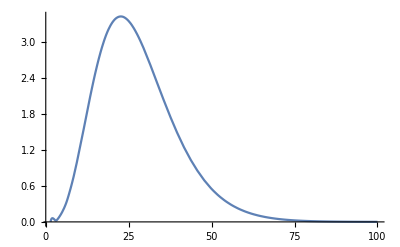

```mathematica
tlmw = {r}|->teuksourcemodal[r]//Evaluate;
rin = {r}|->TeukRin22[r]//Evaluate;
inte = {r}|->tlmw[r]*rin[r]/((0.9^2-2r+r^2)^2);
Plot[inte[r]//Abs, {r,1.44,100}]
```

Comparison of incoming amlitude

```mathematica
SWSHEigenvalue22 = SpinWeightedSpheroidalEigenvalue[-2,2,2,χv*2*Re[ωv]];
binc = IncomingAmplitudeB[RenormedAngMom,2*Re[ωv],χv,2,-2,SWSHEigenvalue22]
```

15.55775716132268861589915947894490178998-1.26878780153470859926966797193895079119 ⅈ

Comparison of Z_lmω

```mathematica
rdom =MySolution["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, MySolution["Parameters", "χ"]]&;
integration = NIntegrate[inte[r]//Re, {r, 4, 221.22222222222223866997073518750521560572`25.},
MaxRecursion->50,
WorkingPrecision->10]
integration/(2*2*Re[ωv]*I*binc)
```

-0.01707633698

-0.0000783781582+0.000961065634 ⅈ

## Output data comparison

```mathematica
TestMass = 0.3;
$root = NotebookDirectory[]<>"../Debugging/NilsSiemonsenCode/OG_Code_MyExecution";
NilsSolutionGW = Import[$root<>"/GWoutput/GW_m1n0_a900000_mu30_prec25.mx"];
NilsSolution = NilsSolutionGW[[10]];
NilsSolution["Derived", "TotalEnergy"] = NilsSolutionGW[[5]];

(*Import my data*)
MySolution = getResults[$SolutionPath, {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[TestMass], InputForm], "/"->"_"]}}]//First;
MySolution["Derived"] = <|"Einf"->MySolution["Derived", "Einf"],"Tlmw"->MySolution["Derived","Tlmw"],"Normalization"->MySolution["Derived","Normalization", "Normalization"],"TotalEnergy"->MySolution["Derived","Normalization","TotalEnergy"],"FinalMass"->MySolution["Derived", "Normalization", "FinalMass"],"FinalSpin"->MySolution["Derived", "Normalization", "FinalSpin"],"Zinf"->MySolution["Derived", "Zinf"]|>;
MySolution["Derived"]["NormalizedEinf"] = MySolution["Derived", "Einf"]/(1-MySolution["Derived", "FinalMass"])^2;
```

```mathematica
DataToCompare = {{"Parameters", "μNv"}, {"Parameters", "m"}, {"Parameters", "n"},{"Solution", "ω"},{"Solution", "ν"},  {"Derived", "Einf"}, {"Derived", "NormalizedEinf"},{"Derived", "TotalEnergy"}, {"Derived", "FinalMass"}, {"Derived", "FinalSpin"}, {"Derived", "Normalization"}};
tabdata = Transpose@Table[ToString[ScientificForm@N@i[Sequence@@j], TraditionalForm], {i,{NilsSolution, MySolution}}, {j,DataToCompare}];
TableView[%, ImageSize->Large, Headers->{{"Nils", "Mine"}, DataToCompare[[All,2]]}, Alignment->Center, ItemSize->20, Scrollbars->False, HeaderSize->7]
```

3.×10^-13.×10^-11.1.0.0.2.83632×10^-1+(4.64801×10^-5) ⅈ2.83632×10^-1+(4.648×10^-5) ⅈ-3.95599×10^-1-(4.24881×10^-5) ⅈ-3.95599×10^-1-(4.24879×10^-5) ⅈ4.81365×10^-84.65387×10^-85.49415×10^-55.31179×10^-52.95985×10^-22.95997×10^-29.704×10^-19.704×10^-18.44919×10^-18.44919×10^-13.38702×10^-33.2172×10^-2